## gdd-gud transition

-(A π)/2+2 B0 π γe+(A d e π ΔE)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))+B0 π γe Δγ-(B0 d e π γe ΔE Δγ)/(√(h^2 Vt^2+d^2 e^2 ΔE^2))-ωB

( | |g↓⇓⟩ | |g↓⇑⟩ | |g↑⇓⟩ | |g↑⇑⟩ | |e↓⇓⟩ | |e↓⇑⟩ | |e↑⇓⟩ | |e↑⇑⟩
|g↓⇓⟩ | -2.86738×10^6 | 0. | 4.39349×10^8 | 0 | 0. | -712.061 | 0 | 0
|g↓⇑⟩ | 0. | 5.82415×10^9 | 0. | 4.39354×10^8 | 0 | 0. | 0 | 0
|g↑⇓⟩ | 4.39349×10^8 | 0. | 1.00584×10^9 | 0. | 0 | -1.12224×10^8 | 0. | 716.952
|g↑⇑⟩ | 0 | 4.39354×10^8 | 0. | 7.49101×10^9 | 0 | 0 | 0 | 0.
|e↓⇓⟩ | 0. | 0 | 0 | 0 | 1.75209×10^10 | 0. | 4.39351×10^8 | 0
|e↓⇑⟩ | -712.061 | 0. | -1.12224×10^8 | 0 | 0. | 2.36416×10^10 | 0. | 4.39352×10^8
|e↑⇓⟩ | 0 | 0 | 0. | 0 | 4.39351×10^8 | 0. | 1.88172×10^10 | 0.
|e↑⇑⟩ | 0 | 0 | 716.952 | 0. | 0 | 4.39352×10^8 | 0. | 2.50148×10^10)

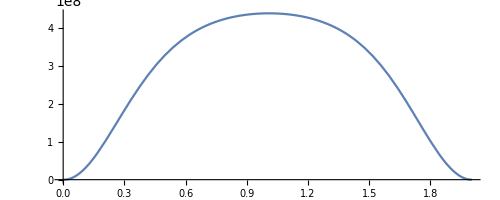

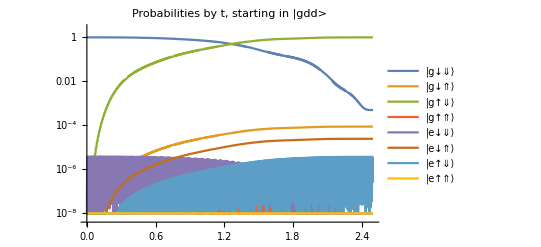

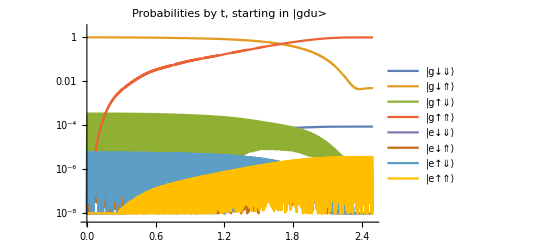

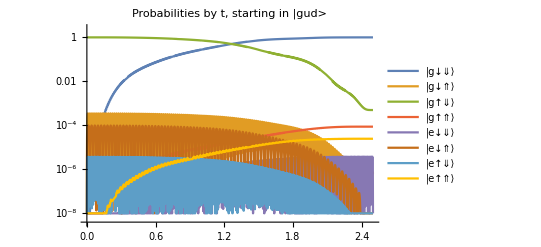

```mathematica
(*H0[[3, 3]] (*- H0[[1, 1]]*) /. {Δγ->0, ωB->2*π*(B0*γe) - 2*π*A*dState[[1]]^2/2} // FullSimplify // Apart
ωB = 2*π*(B0*γe) - 2*π*A*dState[[1]]^2/2;

Δγ = 0;
H0[[3, 3]] // FullSimplify // Apart*)

H0[[3, 3]]

setVariables[]
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-2000,0.2,0,.01,4*^10, 4*^10,25*10^-9};

Δγ = 0;
Clear[ωB]

ωB = 2*π*(B0*γe) - 2*π*A*dState[[1]]^2/2 + map[t/Tmax, -20*10^8, 0*10^8];

Clear[Eamp, Bamp];
Eamp[t_] := Ea*tanhWindow[t, Tmax/5, Tmax]^2;
Bamp[t_] := Ba*tanhWindow[t, Tmax/5, Tmax]^2;

printWithBasis[Hcorrected /. t->Tmax/2, basisGE]

ParametricPlot[{Hcorrected[[3, 3]] - Hcorrected[[1, 1]], Hcorrected[[1, 3]]}, {t, 0, Tmax}]

(*Ubase = MatrixExp[-ⅈ*t*DiagonalMatrix[energiesInOrder[HcorrectedStatic]]];*)

Uax = (*ConjugateTranspose[Ubase].*)findEvolutionOperator[Hexact];
U = Uax/. t->Tmax;

Evaluate@Table[Max[Abs[Uax[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[Uax[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>"]

Evaluate@Table[Max[Abs[Uax[[i]][[3]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gud>"]

clearVariables[]
```

## gdu-edu transition

```mathematica
setVariables[]
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-2000,0.2,0,.01,4*^10, 4*^10,25*10^-9};

Δγ = 0;
Clear[ωE]

ωE = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2/2) + map[t/Tmax, -20*10^8, 0*10^8];

Clear[Eamp, Bamp];
Eamp[t_] := Ea*tanhWindow[t, Tmax/5, Tmax]^2;
Bamp[t_] := Ba*tanhWindow[t, Tmax/5, Tmax]^2;

printWithBasis[Hcorrected /. t->Tmax/2, basisGE]

(*ParametricPlot[{Hcorrected[[6, 6]] - Hcorrected[[2, 2]], Hcorrected[[1, 3]]}, {t, 0, Tmax}]

(*Ubase = MatrixExp[-ⅈ*t*DiagonalMatrix[energiesInOrder[HcorrectedStatic]]];*)

Uax = (*ConjugateTranspose[Ubase].*)findEvolutionOperator[Hexact];
U = Uax/. t->Tmax;

Evaluate@Table[Max[Abs[Uax[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[Uax[[i]][[3]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]*)

clearVariables[]
```

0

( | |g↓⇓⟩ | |g↓⇑⟩ | |g↑⇓⟩ | |g↑⇑⟩ | |e↓⇓⟩ | |e↓⇑⟩ | |e↑⇓⟩ | |e↑⇑⟩
|g↓⇓⟩ | -2.86738×10^6 | 0. | 4.39349×10^8 | 0 | 0. | -712.061 | 0 | 0
|g↓⇑⟩ | 0. | -3.41758×10^10+ωE | 0. | 4.39354×10^8 | 0 | 0. | 0 | 0
|g↑⇓⟩ | 4.39349×10^8 | 0. | 1.00584×10^9 | 0. | 0 | -1.12224×10^8 | 0. | 716.952
|g↑⇑⟩ | 0 | 4.39354×10^8 | 0. | -3.2509×10^10+ωE | 0 | 0 | 0 | 0.
|e↓⇓⟩ | 0. | 0 | 0 | 0 | 5.75209×10^10-ωE | 0. | 4.39351×10^8 | 0
|e↓⇑⟩ | -712.061 | 0. | -1.12224×10^8 | 0 | 0. | 2.36416×10^10 | 0. | 4.39352×10^8
|e↑⇓⟩ | 0 | 0 | 0. | 0 | 4.39351×10^8 | 0. | 5.88172×10^10-ωE | 0.
|e↑⇑⟩ | 0 | 0 | 716.952 | 0. | 0 | 4.39352×10^8 | 0. | 2.50148×10^10)

## gud-edu transition

( | |g↓⇓⟩ | |g↓⇑⟩ | |g↑⇓⟩ | |g↑⇑⟩ | |e↓⇓⟩ | |e↓⇑⟩ | |e↑⇓⟩ | |e↑⇑⟩
|g↓⇓⟩ | -3.69508×10^10 | 0. | 0. | 0 | -8.89757×10^7 | 0 | 0 | 0
|g↓⇑⟩ | 0. | -3.72633×10^10 | 2.9084×10^8 | 0. | 0 | 6.04066×10^7 | -1.49382×10^8 | 0
|g↑⇓⟩ | 0. | 2.9084×10^8 | -2.14913×10^9 | 0. | 0 | -1.49382×10^8 | 8.89757×10^7 | 0
|g↑⇑⟩ | 0 | 0. | 0. | -1.87994×10^9 | 0 | 0 | 0 | -6.04066×10^7
|e↓⇓⟩ | -8.89757×10^7 | 0 | 0 | 0 | 2.04325×10^9 | 0. | 0. | 0
|e↓⇑⟩ | 0 | 6.04066×10^7 | -1.49382×10^8 | 0 | 0. | 1.94487×10^9 | 7.67262×10^7 | 0.
|e↑⇓⟩ | 0 | -1.49382×10^8 | 8.89757×10^7 | 0 | 0. | 7.67262×10^7 | 3.71×10^10 | 0.
|e↑⇑⟩ | 0 | 0 | 0 | -6.04066×10^7 | 0 | 0. | 0. | 3.71551×10^10)

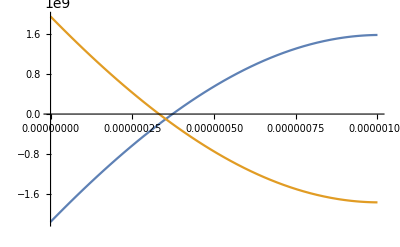

$Aborted

InterpolatingFunction::dmval: Input value {1/1000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

$Aborted

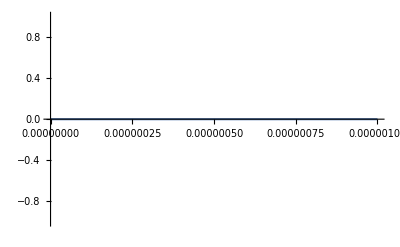

$Aborted

```mathematica
setVariables[]
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-2000,0.2,0,0,4*^10, 4*^10,1000*10^-9};
Vt = Vt*.9;

Clear[Eamp, Bamp];
Eamp[t_] := 0*Ea*tanhWindow[t, Tmax/5, Tmax]^2;
Bamp[t_] := 0*Ba*tanhWindow[t, Tmax/5, Tmax]^2;

(*Δγ = 0;*)

Clear[ΔE]
ΔE = map[t/Tmax, -1000, 0];

printWithBasis[Hexact /. t->0, basisGE]

HexactCopy = Hexact;
Manipulate[
HexactCopy /. t->tt // MatrixForm
,{tt, 0, Tmax}]

Plot[{Hexact[[3, 3]], Hexact[[6, 6]]}, {t, 0, Tmax}]

Uax = (*ConjugateTranspose[Ubase].*)findEvolutionOperator[Hexact];
U = Uax/. t->Tmax;

Evaluate@Table[Max[Abs[Uax[[i]][[3]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gud>"]

Evaluate@Table[Max[Abs[Uax[[i]][[6]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |edu>"]

toEigenbasis[Uin_, Hin_, tIn_?NumericQ] := (
basis = statesInOrder[Hin /. t->tIn];
basis.Uin /. t->tIn
)
Plot[Bamp[t], {t, 0, Tmax}]
LogPlot[{
1 - Abs[toEigenbasis[Uax, Hexact, t][[3, 3]]]^2,
1 - Abs[toEigenbasis[Uax, Hexact, t][[3, 6]]]^2,
1 - Abs[toEigenbasis[Uax, Hexact, t][[6, 3]]]^2,
1 - Abs[toEigenbasis[Uax, Hexact, t][[6, 6]]]^2
}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotRange->{10^-8, Full}]

clearVariables[]
```

## Adiabatic X-gate

{5.59745×10^9,3.39098×10^10,3.37644×10^10}

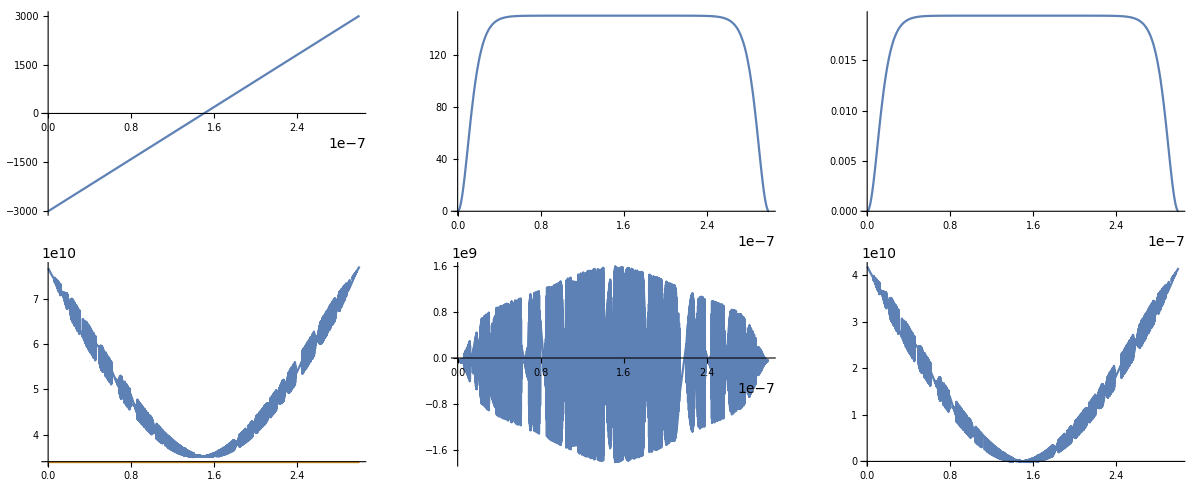

$Aborted

$Aborted

0.985124

0.985124-1.09866×10^-17 ⅈ

( | |g↓⇓⟩ | |g↓⇑⟩
|g↓⇓⟩ | 0.114855-0.0952173 ⅈ | 0.737153+0.659045 ⅈ
|g↓⇑⟩ | -0.962153-0.227901 ⅈ | -0.0124489+0.148652 ⅈ)

$Aborted

$Aborted

```mathematica
(*qqq = H0[[6, 6]] - H0[[3, 3]] // FullSimplify // Apart*)

setVariables[]
(*Δγ = 0;*)
Tmax = 300*10^-9;

ΔEMid = 0;
Δ = 3000;
ΔE = ΔEMid + map[t/Tmax,-Δ, Δ];
B0 = .2;
Do[{Vt = Sqrt[(B0*(γe + γn) - A*dState[[1]]^2/2 + A/4)^2 - ((d*e*ΔEMid)/h)^2] /.ΔE->ΔEMid}, {i, 0, 10}];

ϵ0Mid = ϵ0 /. ΔE->ΔEMid;


(*ωE = 2*π*(ϵ0 + A/4 - A*dState[[1]]^2/2);
ωB = 2*π*(B0*γe - A*dState[[1]]^2/2);*)

Ea =150;
ωE = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2/2) - 12.6*10^8 /. ΔE->ΔEMid;

Ba =Ea*(d*e)/(γe*h);
ωB = 2*π*(B0*γe - A*dState[[1]]^2/2) - 12*10^8 /. ΔE->ΔEMid;

{Vt, ωE, ωB}

Clear[Eamp, Bamp];
Eamp[t_] := Ea*tanhWindow[t, Tmax/20, Tmax]^2;
Bamp[t_] := Ba*tanhWindow[t, Tmax/20, Tmax]^2;


HorbWithShift=TProduct[transform[Vt/2 σX-((e*(ΔE + Eac)*d)/(2h))σZ, ConjugateTranspose[M] // FullSimplify], σI, σI];
HexactWithShift = 2*π*(HB0 + HESR + HA + HorbWithShift) /. {Eac -> Eamp[t]*Cos[ωE*t], Bac -> Bamp[t]*Cos[ωB*t]};


GraphicsGrid[{{Plot[ΔE, {t, 0, Tmax}, PlotRange->All],
Plot[Eamp[t], {t, 0, Tmax}, PlotRange->All],
Plot[Bamp[t], {t, 0, Tmax}, PlotRange->All]},
{Plot[{Hexact[[5, 5]] - Hexact[[1, 1]], ωE}, {t, 0, Tmax}],
Plot[{Hexact[[1, 5]]}, {t, 0, Tmax}],
Plot[Hexact[[6, 6]] - Hexact[[3, 3]], {t, 0, Tmax}]}}, ImageSize->Full]


Manipulate[
Chop[(HexactWithShift - Hexact)  /. t->tt, 10^-5] // MatrixForm
,{tt, 0, Tmax}]


(*Ubase = MatrixExp[-ⅈ*t*DiagonalMatrix[energiesInOrder[HexactStatic /. t->0]]];*)
Uax = (*(ConjugateTranspose[Ubase])[[{1, 2}, {1, 2}]].*)findEvolutionOperator2D[Hcorrected];
U = Uax/. t->Tmax;



F = fidelityXY[U[[{1, 2}, {1, 2}]]] // Chop;
targetGate = Cos[XYangle[U[[{1, 2}, {1, 2}]]]]*σX + Sin[XYangle[U[[{1, 2}, {1, 2}]]]]*σY;
Print[F]
Print[fidelity2D[targetGate, U[[{1, 2}, {1, 2}]]]]
printWithBasis[U, basisGE]

Evaluate@Table[Max[Abs[Uuncut[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[Uuncut[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>"]

(*Clear[Δγ]
Δγ=0;
H0 /.  {Δγ->0, t->0} // MatrixForm
*)

clearVariables[]
```

### Mess around with the supposedly faster way of turning on Bac

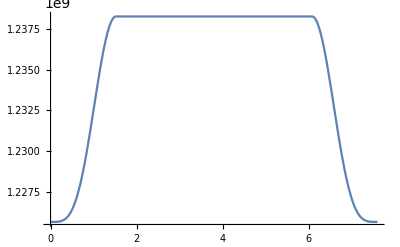

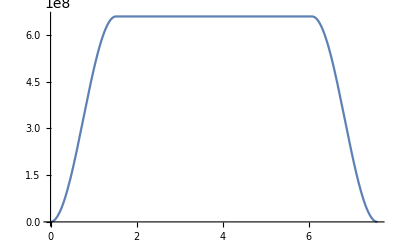

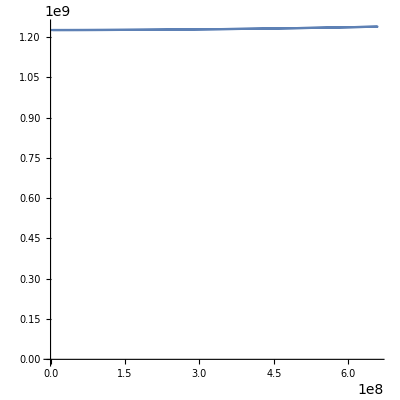

(0 | 0 | 4.86345×10^8 | 0 | 0. | 0 | 0 | 0
0 | 6.58837×10^9 | 0 | 4.86345×10^8 | 0 | 0. | 0 | 0
4.86345×10^8 | 0 | 1.22546×10^9 | 0 | 0 | -1.54235×10^8 | 0. | 0
0 | 4.86345×10^8 | 0 | 7.98152×10^9 | 0 | 0 | 0 | 0.
0. | 0 | 0 | 0 | 1.51006×10^9 | 0 | 4.86345×10^8 | 0
0 | 0. | -1.54235×10^8 | 0 | 0 | 7.89855×10^9 | 0 | 4.86345×10^8
0 | 0 | 0. | 0 | 4.86345×10^8 | 0 | 2.49742×10^9 | 0
0 | 0 | 0 | 0. | 0 | 4.86345×10^8 | 0 | 9.45335×10^9)

0.0000501234+0. ⅈ

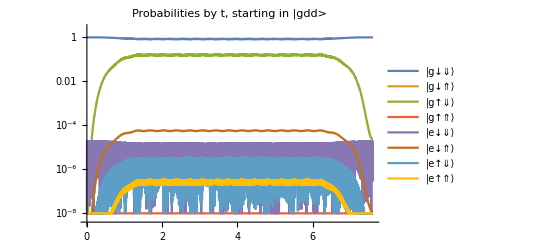

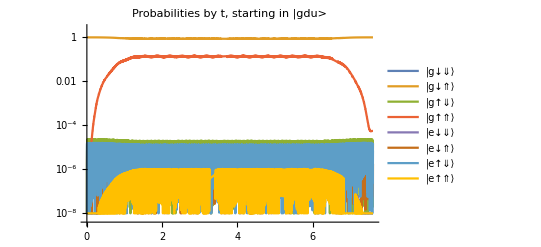

```mathematica
clearVariables[]
setVariables[]

T1a = 10*10^-9;
T1b = 3*10^-9;
T2 = 50*10^-9;
Tmax = 2*T1a + 2*T1b + T2;

ΔE = 1000;

EaD =0*200;
ωED = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2/2) - 2*π*2.0548*10^8 /. ΔE->ΔEMid;

BaD = 0.015;
BaDmax = .1;
ωBD = 2*π*(B0*γe - A*dState[[1]]^2/2) - 2*π*1.9759*10^8 /. ΔE->ΔEMid;
ωBmax = ωBD - 3*10^9;

(*fidelityToGate[EaD, BaD, ωED, ωBD, "XY"]*)
Clear[Eamp, Bamp];
Eamp[t_] := 0;
Bamp[t_] := Piecewise[{
{BaDmax*t/T1a, t < T1a},
{BaDmax - (BaDmax - BaD)*(t - T1a)/T1b, T1a ≤ t < T1a + T1b},
{BaD, T1a + T1b ≤ t < T1a + T1b + T2},
{BaDmax - (BaDmax - BaD)*(Tmax - T1a - t)/T1b, Tmax - T1a - T1b ≤ t < Tmax - T1a},
{BaDmax*(Tmax - t)/T1a, Tmax - T1a ≤ t < Tmax}
}, 0];

ωE = ωED;
ωB = Piecewise[{
{ωBmax, t < T1a},
{ωBmax - (ωBmax - ωBD)*(t - T1a)/T1b, T1a ≤ t < T1a + T1b},
{ωBD, T1a + T1b ≤ t < T1a + T1b + T2},
{ωBmax - (ωBmax - ωBD)*(Tmax - T1a - t)/T1b, Tmax - T1a - T1b ≤ t < Tmax - T1a},
{ωBmax, Tmax - T1a ≤ t < Tmax}
}, ωBmax];

Bamp[t_] := BaD*cosWindow[t, Tmax/5, Tmax];
ωB = ωBD;

a = Hcorrected[[3, 3]] - Hcorrected[[1, 1]];
b = H0[[1, 3]];

Plot[a, {t, 0, Tmax}, PlotRange->All]
Plot[b , {t, 0, Tmax}, PlotRange->All]
ParametricPlot[Piecewise[{{{b, a}, t>Tmax/100}}, {0, 0}], {t, 0, Tmax}, AspectRatio->1,PlotRange->All]

H0 /. t->T1a // MatrixForm

U = findEvolutionOperator2D[Hexact, Tmax];
(*U = (Λge /. t->t).findEvolutionOperator[HexactID, Tmax].ConjugateTranspose[Λge /. t->0];
Uuncut = U;*)

1 - Tr[(U.ConjugateTranspose[U])/2 /. t->Tmax]

Evaluate@Table[Max[Abs[Uuncut[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[Uuncut[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>"]
```

### Full sneaky X-gate, unoptimized

0.996749

{0.996749,{10300-12000 twoPointWindow[t,1/200000000,3/25000000,2/3],0.2,5.59745×10^9,244,0.0318,3.37674×10^10,3.36582×10^10,3/25000000}}

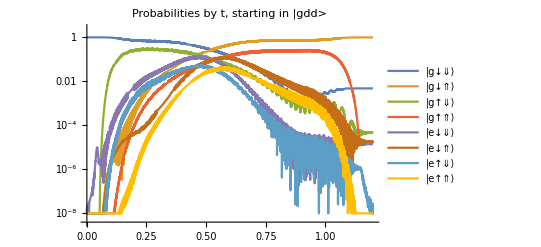

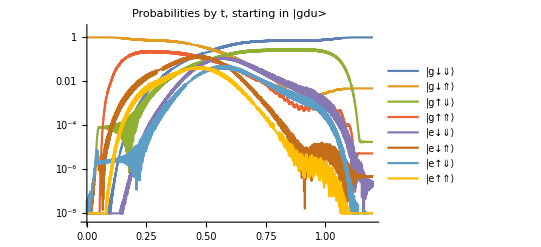

```mathematica
setVariables[]

T1 = 5*10^-9;
T2 = 110*10^-9;
Tmax = 2*T1 + T2;

ΔEMid = 0;
Δ = 2000;
ΔE = 10000 - 12000*twoPointWindow[t, T1, Tmax, 8/12] + 300;
ϵ0Mid = ϵ0 /. ΔE->ΔEMid;

EaD =244;
ωED = 3.3767399946666843*^10;

BaD = .0318;
ωBD = 3.365817946982966*^10;

Eamp[t_] := Ea*cosWindow[t - T1, T2/5, T2];
Bamp[t_] := Ba*cosWindow[t - T1, T2/5, T2];

(*fidelityToGate[EaD, BaD, ωED, ωBD, "XY"]*)
Clear[Eamp, Bamp];
Eamp[t_] := EaD*cosWindow[t - T1, T2/5, T2];
Bamp[t_] := BaD*cosWindow[t - T1, T2/5, T2];
ωE = ωED;
ωB = ωBD;

(*extraTerm = 10^0*(d*e*Vt/(2*h*ϵ0^2))*ND[ΔE, t, t - Tmax/2, Scale->10^-9, Terms->1];
Plot[extraTerm, {t, 0, Tmax}]
Plot[extraTerm, {t, 0, Tmax}, PlotRange->All]*)

U = findEvolutionOperator2D[Hexact(* + extraTerm*TProduct[σY, σI, σI]*), Tmax];
(*U=(Λge /. t->t).findEvolutionOperator[HexactID, Tmax].ConjugateTranspose[Λge /. t->0];*)
fidelityXY[U[[{1, 2}, {1, 2}]] /. t->Tmax]

Print[{%, {ΔE, B0,Vt, EaD, BaD, ωED, ωBD, Tmax}}];

Evaluate@Table[Max[Abs[Uuncut[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[Uuncut[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>"]
```

{0.999893,{10000-12000 twoPointWindow[t,1/200000000,3/25000000,2/3],0.2,5.59745×10^9,244.153,0.0318473,3.37674×10^10,3.36582×10^10,3/25000000}}

0.999893

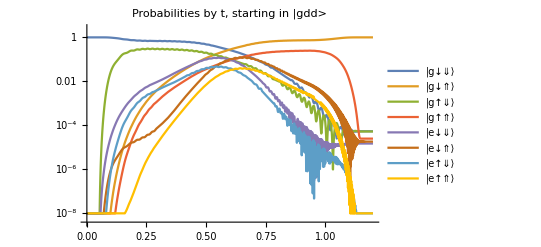

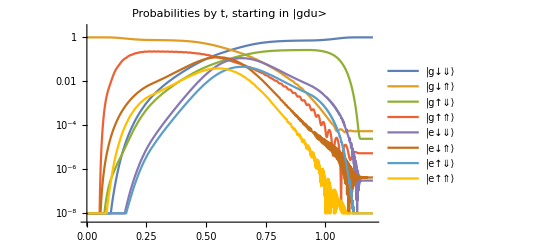

```mathematica
fidelityToGate[EaD, BaD, ωED, ωBD, "XY"]

Evaluate@Table[Max[Abs[Uuncut[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[Uuncut[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>"]
```